```mathematica
MatrixForm[A = {{0,0},{1,8},{3,8},{4,20}}]
```

(0 | 0
1 | 8
3 | 8
4 | 20)

```mathematica
MatrixForm[standardA=Standardize[A,Mean,1&]]
```

(-2 | -9
-1 | -1
1 | -1
2 | 11)

```mathematica
Transpose[standardA].standardA
```

{{10,40},{40,204}}

```mathematica
Eigensystem[Transpose[standardA].standardA]
```

{{107+√11009,107-√11009},{{1/40 (-97+√11009),1},{1/40 (-97-√11009),1}}}

```mathematica
N[107-√11009]
```

2.07622

```mathematica
a=40;
b=90-Sqrt[11009];
c=-953+9 Sqrt[11009];
f[x_]:=(40 x)/(-97+Sqrt[11009])+9-80/(-97+Sqrt[11009]);
```

```mathematica
MatrixForm[N[Table[{Abs[a A⟦i,1⟧+b A⟦i,2⟧+c]/Sqrt[a^2+b^2],Abs[A⟦i,2⟧-f[A⟦i,1⟧]]},{i,4}]]]
```

(0.20345 | 1.09619
2.063 | 4.04809
0.189168 | 6.04809
3.44695 | 0.903811)

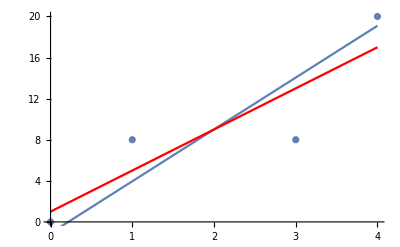

```mathematica
Show[ListPlot[Table[A⟦i⟧,{i,4}]],Plot[f[x],{x,0,4}],Plot[1+4 x,{x,0,4},PlotStyle->Red]]
```